```mathematica
x1+y1/.Flatten[{{x1->0.1},{y1->0.9}}]
```

1.

```mathematica
p+x/.{p->0.1,x->0.4}
```

0.5

```mathematica
a=2;
b=-1;
T=1;
Flatten[Take[FindMinimum[Abs[(a p +b)-2 T Log[p/(1-p)]],{p,0.95}],-1]]
```

{p→0.5}

```mathematica
Prisoner's Dilemma game: Eigenvalues and stable region of homogenouse netwrok
```

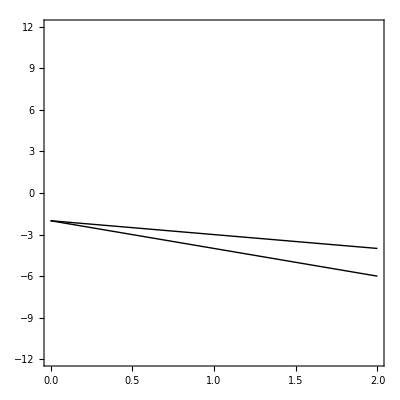

```mathematica
Clear[a,b,d,cp,T,a22,p]
a11=3+cp;a12=0+cp;a21=4+cp;a22=2+cp;
a=a11-a21-a12+a22;
b=a12-a22;
d=a21-a22;


c4=ContourPlot[{{1/2 (-a22-p (b+d+a p)-2 T),-a22-p-T}/.{{p->0}}}==0,{T,0,2},{cp,-12,12},ContourStyle->{Black}];

picf=Show[c4,PlotRange->{{0.0,2},{-12,12}}]
Export["stable_pd.eps",Rasterize[picf,RasterSize->400,ImageResolution->800]];
```

```mathematica
T=0.8;
A={{3,0},{4,2}};
B={{3,0},{4,2}};
CC={{3,0},{4,2}};
a=A[[1,1]]-A[[2,1]]-A[[1,2]]+A[[2,2]];
b=A[[1,2]]-A[[2,2]];
d=A[[2,1]]-A[[2,2]];
a22=2;
Clear[x1,y1,z1,cxy,czx,cyz,cp];
czx=1/2;
FindRoot[{
Re[(1-x1)x1((a x1+b)cxy (1-cyz)+ (a z1+b) ( 1-cxy) czx+  T Log[(1-x1)/x1])],
Re[(1-z1)z1((a x1+b)czx (1-cxy)+ (a x1+b) cyz( 1- czx)+ T Log[(1-z1)/z1])],
Re[cxy(1-cxy)((a x1 x1+ b x1+d x1+a22) (1-cyz)- (a x1 z1+ b x1+d z1+a22) czx +T Log[(1-cxy)/cxy])],
Re[cyz(1-cyz)((a x1 z1+ b x1+d z1+a22) (1-czx)- (a x1 x1+ b x1+d x1+a22) cxy +T Log[(1-cyz)/cyz])]},
{x1,RandomReal[]},{z1,RandomReal[]},{cxy,RandomReal[]},{cyz,RandomReal[]}]
```

{x1→1.,z1→0.266215,cxy→-4.07675×10^-10,cyz→0.62226}

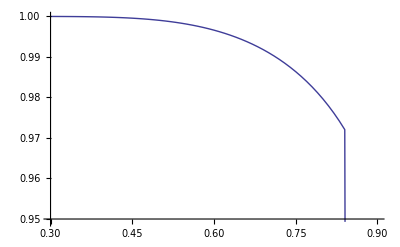

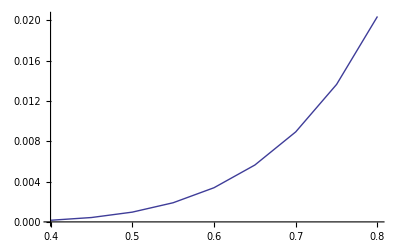

```mathematica
ListLinePlot[{{0.30,0.9999914109356695},{0.31,0.9999874790729332},{0.32,0.9999821691511124},{0.33,0.9999751406590485},{0.34,0.9999660048237715},{0.35,0.999954323849611},{0.36,0.9999396107128401},{0.37,0.9999213294266943},{0.38,0.9998988956803008},{0.39,0.9998716777501866},{0.40,0.9998389975839395},{0.41,0.9998001319603955},{0.42,0.9997543136383613},{0.43,0.9997007324152218},{0.44,0.9996385360264209},{0.45,0.9995668308266149},{0.46,0.9994846822019733},{0.47,0.9993911146708213},{0.48,0.999285111636008},{0.49,0.9991656147569508},{0.50,0.9990315229123413},{0.51,0.9988816907256909},{0.52,0.9987149266256485},{0.53,0.9985299904109453},{0.54,0.9983255902862913},{0.55,0.9981003793301789},{0.56,0.9978529513486207},{0.57,0.9975818360599195},{0.58,0.9972854935445962},{0.59,0.9969623078813141},{0.60,0.9966105798734416},{0.61,0.9962285187515494},{0.62,0.9958142327135562},{0.63,0.9953657181358339},{0.64,0.9948808472539027},{0.65,0.9943573540688918},{0.66,0.9937928181836485},{0.67,0.9931846462074888},{0.68,0.9925300502874506},{0.69,0.9918260232218837},{0.70,0.9910693094825649},{0.71,0.9902563713058445},{0.72,0.9893833487993056},{0.73,0.9884460127317144},{0.74,0.9874397083072419},{0.75,0.9863592877373579},{0.76,0.9851990287678778},{0.77,0.9839525354258156},{0.78,0.9826126160185971},{0.79,0.9811711316935842},{0.80,0.9796188064126804},{0.81,0.9779449856461734},{0.82,0.9761373258504923},{0.83,0.9741813888949968},{0.84,0.9720601034027306},{0.85,0.5000000125086953},{0.86,0.4999999993940662},{0.87,0.5000000000115018},{0.88,0.4999999999908562},{0.89,0.5000000000053086},{0.9,0.500000000011921}}]
ListLinePlot[{{0.4,0.00016100241605949316},{0.45,0.0004331691733852555},{0.5,0.0009684770876584244},{0.55,0.0018996206698221212},{0.6,0.0033894201265581496},{0.65,0.005642645931108147},{0.7,0.008930690517434326},{0.75,0.013640712262642745},{0.8,0.020381193587319008}}]
```

FindMinimum::nrnum: The function value Abs[0.5  - 5.96046×10^-8\ T]
 is not a real number at {x1} = {0.5}.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

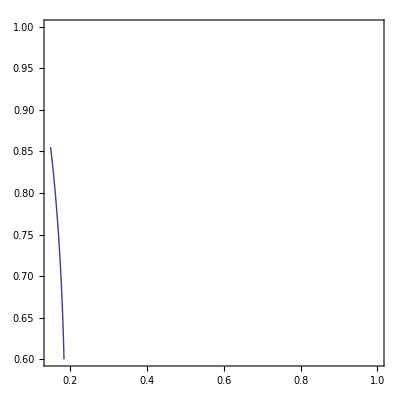

```mathematica
Clear[t,T,e,x1,y1,z1,cxy,cyz,czx,x0,y0,z0,cxy0,cyz0,czx0,rx,ry,rz,rcxy,rcyz,rczx,Rx,Ry,Rz,tmax]
A={{a11,a12},{a21,a22}};
B={{b11,b12},{b21,b22}};
CC={{c11,c12},{c21,c22}};
PD;
(*a11=3;a12=0;a21=4;a22=2;
b11=3;b12=0;b21=4;b22=2;
c11=3;c12=0;c21=4;c22=2;*)
cp=2;
a11=6-cp;a12=0-cp;a21=3-cp;a22=2-cp;
b11=6-cp;b12=0-cp;b21=3-cp;b22=2-cp;
c11=6-cp;c12=0-cp;c21=3-cp;c22=2-cp;
a=a11+a22-a12-a21;
b=a12-a22;
d=a21-a22;
ContourPlot[{Re[cxy(1-cxy)((a x1 x1+ b x1+d x1+a22) (cxy)- (a x1 (1/2)+ b x1+d (1/2)+a22) (1/2) +T Log[(1-cxy)/cxy])]/.Take[FindMinimum[Abs[(a x1 +b)- T Log[x1/(1-x1)]],{x1,0.5}],-1]}==0,{T,0.15,1},{cxy,0.6,1},PlotPoints->50]
```

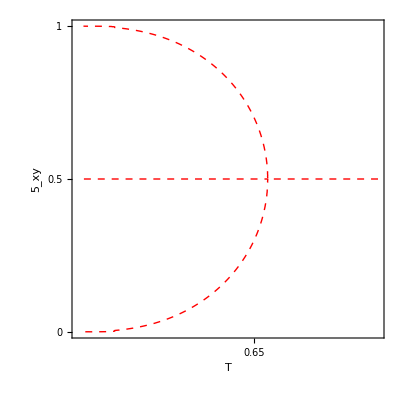

```mathematica
ContourPlot[Re[cxy(1-cxy)(-1.375+2.75 (cxy)+T Log[(1-cxy)/cxy])]==0,{T,0.15,1},{cxy,0,1},PlotPoints->50,ContourStyle->{Red,Dashed,Thick},FrameTicks->{{{0,0.5,1},None},{{0,0.65},None}},FrameStyle->Directive[23],FrameLabel->{T,Subscript[c,xy]}]
```

```mathematica
A={{6,0},{3,2}};
B={{6,0},{3,2}};
a=A[[1,1]]+A[[2,2]]-A[[1,2]]-A[[2,1]]
b=A[[1,2]]-A[[2,2]]
c=B[[1,1]]+B[[2,2]]-B[[1,2]]-B[[2,1]]
d=B[[1,2]]-B[[2,2]]

f1=ContourPlot[-b/a+T/a(Log[(-d/c+T/c(Log[y/(1-y)]))/(1-(-d/c+T/c(Log[y/(1-y)])))])==y,{T,0.2,2},{y,0.5,1},FrameTicks->{{{1},None},{{0,2},None}},FrameStyle->Directive[23],FrameLabel->{T,x},ContourStyle->{Thickness[0.01],Blue},PlotPoints->260];
f2=ContourPlot[-b/a+T/a(Log[(-d/c+T/c(Log[y/(1-y)]))/(1-(-d/c+T/c(Log[y/(1-y)])))])==y,{T,0.2,2},{y,0.18,0.5},FrameTicks->{{{1},None},{{0,2},None}},FrameStyle->Directive[23],FrameLabel->{T,x},ContourStyle->{Thickness[0.01],Red, Dashed},PlotPoints->60];
f3=ContourPlot[-b/a+T/a(Log[(-d/c+T/c(Log[y/(1-y)]))/(1-(-d/c+T/c(Log[y/(1-y)])))])==y,{T,0.2,2},{y,0,0.18},FrameTicks->{{{1},None},{{0,2},None}},FrameStyle->Directive[23],FrameLabel->{T,x},ContourStyle->{Thickness[0.01],Blue},PlotPoints->260];

picf=Show[f1,f2,f3,PlotRange->{{0.2,2},{0,1}},FrameTicks->{{{0,1},None},{{0,0.75,2},None}}]
Export["bifo.pdf",Rasterize[picf,RasterSize->400,ImageResolution->800]];
```

5

-2

5

-2

5

-2

5

-2

4.7

-2

4.7

-2

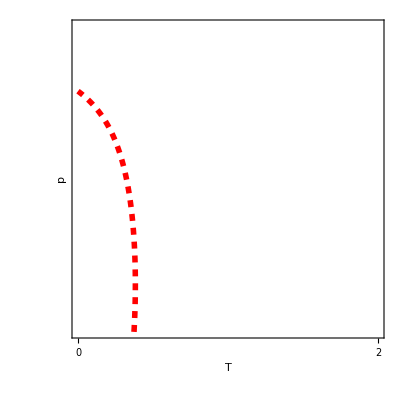

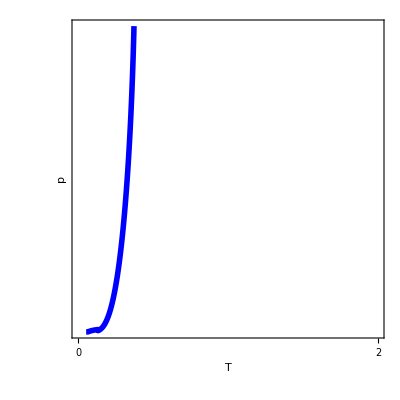

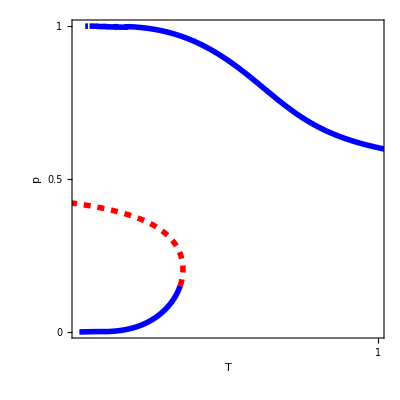

stable_co.pdf

```mathematica
A={{6,0},{3,2}};
B={{6,0},{3,2}};
a=A[[1,1]]+A[[2,2]]-A[[1,2]]-A[[2,1]]
b=A[[1,2]]-A[[2,2]]
c=B[[1,1]]+B[[2,2]]-B[[1,2]]-B[[2,1]]
d=B[[1,2]]-B[[2,2]]
a=4.7
b=-2
c=4.7
d=-2

f1=ContourPlot[2 T Log[p/(1-p)]==a p +b,{T,0,2},{p,0.5,1},FrameTicks->{{{1},None},{{0,2},None}},FrameStyle->Directive[23],FrameLabel->{T,p},ContourStyle->{Thickness[0.01],Blue},PlotPoints->60];
f2=ContourPlot[2 T Log[p/(1-p)]==a p +b,{T,0,2},{p,0.15,0.5},FrameTicks->{{{1},None},{{0,2},None}},FrameStyle->Directive[23],FrameLabel->{T,p},ContourStyle->{Thickness[0.01],Red, Dashed},PlotPoints->60]
f3=ContourPlot[2 T Log[p/(1-p)]==a p +b,{T,0,2},{p,0.,0.15},FrameTicks->{{{1},None},{{0,2},None}},FrameStyle->Directive[23],FrameLabel->{T,p},ContourStyle->{Thickness[0.01],Blue},PlotPoints->60]
picf=Show[f1,f2,f3,PlotRange->{{0.05,1},{0,1}},FrameTicks->{{{0,0.5,1},None},{{0,1},None}}]
Export["stable_co.pdf",Rasterize[picf,RasterSize->400,ImageResolution->800]]
```